2

复变函数的积分

## 2.1 积分的定义和性质

### 复变函数积分的定义

类似于实变函数，可定义复变函数的积分。

定义：设函数 f(z) 在光滑或分段光滑的曲线  L 上有定义，则 f(z) 沿 L 路线积分定义如下：

把曲线 L分成 n 段，在每段 z_k-z_(k-1)=Δ z_k间任取一点 ξ_k，若求和式

S_n=(∑^n)_(k=1)f(ξ_k)Δ z_k  的极限  lim_(max{|Δ z_k|}→0) S_n=∫_L f(z)ⅆz

存在，则称极限值为 f(z) 在 L上的积分，记为： ∫_L f(z)ⅆz。

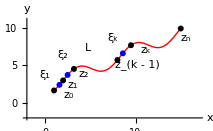
-Graphics-      \[MathematicaIcon] Mathematica  作图源代码参见：
code02.01 definition of integral.nb

注意：  {复函数积分：极限的存在必须与  1.  弧段的分法；2.  ξ_k 在 z_(k-1)到  z_k 间的取法 无关
实函数积分：极限的存在必须与  1.  线段的分法；2.  ξ_k  在 x_(k-1) 到 x_k 间的取法 无关

### 复变函数积分的计算

化为两个二元实变函数的第二类（对坐标的）曲线积分

∫_L f(z)ⅆz=lim_(max|Δ x_k|→0
max|Δ y_k|→0) (∑_(k=1))^n(u_k+ⅈ v_k)(Δx_k+ⅈ Δy_k)=lim_(max|Δ x_k|→0
max|Δ y_k|→0) (∑_(k=1))^n[u_k Δ x_k-v_k Δ y_k+ⅈ(u_k Δ y_k+v_k Δ x_k)]

∫_L f(z)ⅆz=∫_L (uⅆx-vⅆy)+ⅈ∫_L (uⅆ y+vⅆx)                 两个第二类曲线积分

若曲线 L 由参数方程确定，则可化为参数方程的积分

曲线 L：Piecewise[{{x=x(t), }, {y=y(t), }}],            ∫_L f(z)ⅆz=∫_L f[z(t)]ⅆz(t)=(∫_t_1)^t_2 f[z(t)]z'(t)ⅆt

⟹   实部与虚部两个一元函数的积分

### 复变函数积分的性质

若曲线 L=L_1+L_2+... +L_n，则

∫_L f(z)ⅆz=(∑_(k=1))^n ∫_L_k f(z)ⅆz

若曲线 L 与 L^- 反向，则

∫_L f(z)ⅆz=-∫_(L^-) f(z)ⅆz

线性：

∫_L [a_1 f_1(z)±a_2 f_2(z)]ⅆz=a_1∫_L f_1(z)ⅆz±a_2∫_L f_2(z)ⅆz，其中 a_1, a_2 为常复数

不等式（在证明一个积分为 0 时常用到）

|∫_L f(z)ⅆz|≤ ∫_L |f(z)|  |ⅆz|

证明：

|(∑_(k=1))^n f(ξ_k)Δ z_k|≤ (∑_(k=1))^n |f(ξ_k)| |Δ z_k|,   两边取极限即得

上限：若 M 为 |f(z)| 在曲线 L 上的上界，则

|∫_L f(z)ⅆz|≤ M l,                   l 为曲线 L 的长度

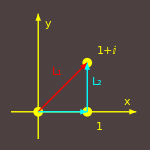
```mathematica
{{-Graphics-, □}}
```

例题： I = ∫_L Re z ⅆz，L 为： L_1 从原点到 1+ⅈ 的直线； L_2 从原点到 1，再到 1+ⅈ

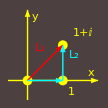
沿 L_1： z=r ⅇ^(ⅈ π/4), 
I=(∫_0)^(√2)r cos π/4 ⅆ(r ⅇ^(ⅈ π/4))
   =(∫_0)^(√2)r  ⅇ^(ⅈ π/4)cos π/4 ⅆr=1/2(1+ⅈ)          -Graphics-

其中利用了复变函数的求导法则与实变函数同：ⅆz(t)=z'(t)ⅆt,    ⅆ(r ⅇ^(ⅈ π/4))= ⅇ^(ⅈ π/4)ⅆr

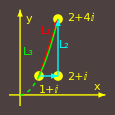
沿 L_(2：)     
I=(∫_0)^1 x ⅆ x +(∫_0)^1 1 ⅆⅈ y
    =1/2+ⅈ                                     -Graphics-

对本题的积分，积分路径不同时，积分值不同。

例题： I = ∫_L z^2 ⅆz，L 为： L_1  从 1+ⅈ 到 2+4ⅈ 的直线；

L_2  沿直线 1+ⅈ 到 2+ⅈ，再到 2+4ⅈ；

L_3  从 1+ⅈ 沿过 0,  1+ⅈ,  2+4ⅈ  的抛物线到 2+4ⅈ

沿 L_(1：)直线方程：y=3x-2,

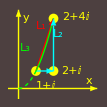
⟹   I=∫(x+ⅈ y)^2 ⅆ(x+ⅈ y)，以 y=3x-2 代入
=∫_1^2 [x+ⅈ (3x-2)]^2 ⅆ[x+ⅈ (3x-2)]
=∫_1^2 [(1+3ⅈ)x-2ⅈ]^2(1+3ⅈ)ⅆx= -86/3-6ⅈ     -Graphics-

沿 L_(2：)第一段   y=1， ⅆy=0，   I_1=(∫_1)^2(x+ⅈ )^2 ⅆx=4/3+3 ⅈ，

第二段：x=2， ⅆx=0， I_2=(∫_1)^4 (2+ⅈ y)^2 ⅆ(ⅈ y)=-30-9ⅈ

I=I_1+I_2=-86/3-6ⅈ

沿 L_(3：)抛物线方程：y=x^2 代入

I=∫_(x=1)^(x=2) (x+ⅈ y)^2 ⅆ(x+ⅈ y)=∫_(x=1)^(x=2) (x+ⅈ x^2)^2 ⅆ(x+ⅈ x^2)，利用  ⅆ(x+ⅈ x^2)=(1+2ⅈ x)ⅆx

I=∫_(x=1)^(x=2) (x+ⅈ x^2)^2(1+2x ⅈ)ⅆx=∫_(x=1)^(x=2) (x^2+4 ⅈ x^3-5 x^4-2 ⅈ x^5)ⅆx=-86/3-6ⅈ

对本题的积分，积分路径不同时，积分值相同。

在什么情况积分值才与积分路径无关？ ——  看成二元实变函数的第二类曲线积分

∫_L f(z)ⅆz=∫_L (u+ⅈ v)ⅆ(x+ⅈ y)=∫_L (u+ⅈ v)(ⅆx+ⅈ ⅆy
=∫_L (uⅆx-vⅆy)+ⅈ∫_L (uⅆy+vⅆx)

⟹   两个实变二元函数的第二类曲线积分

实二元函数第二类曲线积分 ∫_L (Pⅆx+Qⅆy)

积分值与积分路径无关的条件：P_y=Q_x

⟹^应用到复积分  若 u, v 满足 C-R   条件，则积分就可能与路径无关 。

\[FreakedSmiley]  是否解析函数的积分与路径无关？充分？必要？还需要什么条件？

其它条件：单连通有界区域？一阶偏导数连续？将在下一节的 Cauchy 定理中讨论。

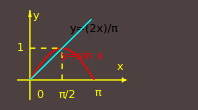
-Graphics-          -Graphics-

例题： 若 z 在上半平面及沿实轴趋于 ∞ 时， z f(z) 一致趋于 0（与 z 趋于 ∞ 的辐角无关，

只要其辐角 θ=arg z 满足 0≤ θ≤π），即

如果：        lim_(z→∞) z f(z)=0,     0≤ θ=arg z ≤π,

则：沿上半平面任意一段圆心于原点半径为 R 的圆弧：  lim_(R→∞) ∫_C_R f(z) ⅆz =0

证明：这是第一次遇到求证积分为 0 的问题，今后证明复积分为 0，方法多与此相似。

要证明积分值为 0，只需证明积分值的模为 0。常利用 |∫_L f(z)ⅆz|≤ ∫_L |f(z)| |ⅆz|，下证之。

|∫_C_R f(z) ⅆz |≤ ∫_C_R |f(z)| |ⅆz| =I，需证明：lim_(R→∞) I=0

在 C_R 上：z=R ⅇ^(ⅈ θ)   ⟹    ⅆz=R ⅈ ⅇ^(ⅈ θ)ⅆθ   ⟹    |ⅆz| =R|ⅆθ|    ⟹   |ⅆz|=|z||ⅆθ|

I=∫_C_R |f(z)| × |z| |ⅆθ|=∫_C_R |z f(z)| |ⅆθ| < ε ∫_C_R |ⅆθ|=ε |θ_2-θ_1|

其中因为： lim_(z→∞) z f(z)=0，故 ∀ε>0，可找到 R'，使得当 |z|>R' 时， |z f(z)|<ε，

现取 R>R'，则有： ∫_C_R |z f(z)||ⅆθ|<  ε ∫_C_R|ⅆθ|

也就是说，无论给定多么小的 ε>0，均可找到一个 R'', 当 R>R'' 时，0<I<ε

或更简单地，写成

I =∫_C_R |z f(z)|(|ⅆz|)/(|z|)≤ max |z f(z)|∫_θ_1^θ_2 |ⅆθ|=max|z f(z)| × |θ_2-θ_1|,

R→∞ 时，z f(z) →0，故    max|z f(z)|  可小于任意小量。即：I>0 可以小于任意小

例题： Jordan 引理：若 z 在上半平面及实轴上趋于 ∞ 时， f(z) 一致趋于 0，即

lim_(z→∞) f(z)=0,     0≤ θ=arg z ≤π,

则沿上半平面任意一段圆心于原点半径为 R 的圆弧：  lim_(R→∞) ∫_C_R f(z) ⅇ^(ⅈ m z)ⅆz =0，其中  m>0

证明：方法类似于上一题。在大圆弧 C_R 上，

z=R ⅇ^(ⅈ θ)   ⟹   ⅆz=R ⅈ ⅇ^(ⅈ θ)ⅆθ    ⟹    |ⅆz| =R|ⅆθ|    ⟹   |ⅆz|=|z||ⅆθ|

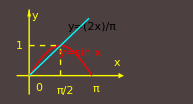
|∫_C_R f(z) ⅇ^(ⅈ m z)ⅆz |≤ ∫_C_R |f(z)| |ⅇ^(ⅈ m z)| |ⅆz| =I    
接着证明 I 可小于任意小的正数
因为 z 为复数，|ⅇ^(ⅈ m z)|≠1，而是 |ⅇ^(ⅈ m z)|=|ⅇ^(ⅈ m (R cos θ + ⅈ R sin θ))|=ⅇ^(-m R sin θ)
 I=∫_C_R |f(z)|× ⅇ^(-m R sin θ)R|ⅆθ| ≤  ε R ∫_θ_min^θ_max ⅇ^(-m R sin θ)|ⅆθ|
注意此时 ε→0, 但 R→∞,  不能确定  ε R →0,  故需要算出对 θ 的积分。  -Graphics-

对辐角大于 π/2 的那一段圆弧，可通过变换  ϕ=π-θ 化为一段辐角在 0 到 π/2 之间的积分，

例如：∫_(π/2)^π ⅇ^(-m R sin θ)|ⅆθ|   ⟹^(ϕ =π-θ)  ∫_0^(π/2) ⅇ^(-m R sin ϕ)|ⅆϕ|

对任一段辐角在 0 到 π/2 之间的积分，利用0≤θ≤π/2时有sin θ >2/π θ,

故：∫_θ_min^θ_max ⅇ^(-m R sin θ)|ⅆθ|≤ ∫_θ_min^θ_max ⅇ^(-m R 2/π θ)ⅆθ=(π(ⅇ^(- m R θ_min)-ⅇ^(- m R θ_max)))/(2m R)

代入 I  可得：I =π ε R (ⅇ^(- m R θ_min)-ⅇ^(- m R θ_max))/(2m R)=(π ε)/(2m)(ⅇ^(- m R θ_min)-ⅇ^(- m R θ_max)) →0

若 m<0，lim_(R→∞) ∫_C_R f(z) ⅇ^(ⅈ m z)ⅆz =0 则要求当 z 在下半平面趋于 ∞ 时，f(z) 一致趋于 0。

上一章提到的积分：∫_(-∞)^-1 (x-√(x^2-1))^17 ⅇ^(-1/2 √(x^2-1))cos(17x) d x，就是利用 π/2<θ≤π 的任一段大圆弧上 C_R 上的积分为 0。

当然还要利用一个闭合回路的积分为 0 把积分化为沿 z+1=r ⅇ^(ⅈ θ_0) （固定 θ_0=2/3 π，r 从 0 到无穷）进行。

至于什么条件下沿闭合路径积分为 0，下一节就将讨论。

本节最后两个例题，其实是两个定理，在以后求积分时会常常用到。简而言之，为：

若：lim_(z→∞) z f(z)=0

⟹    lim_(R→∞) ∫_C_R f(z) ⅆz =0               此定理可视为大圆弧引理（见后）的特殊情况

若：lim_(z→∞) f(z)=0

⟹    lim_(R→∞) ∫_C_R f(z) ⅇ^(ⅈ m z)ⅆz =0      { 若 m>0，则 C_R 应在上半平面
若 m<0，则 C_R 应在下半平面 }

以保证  Re (ⅈ m z)<0

思考：以上表述漏了什么细节？

## 2.2 Cauchy 定理

复变函数的积分实际上为两个二元实变函数的第二类（对坐标的）曲线积分。

那么，在什么条件下，积分值与积分路径无关？—— 似乎可借助于二元实变函数的知识。

先来点感觉 —— 参见 \[MathematicaIcon] Mathematica 程序 code02 .04 ContourIntegration.nb。

从这些积分可知，积分值是否与积分路径有关，至少取决于：被积函数的性质和积分路径本身。

借助于二元实变函数的理论 —— 二元实变函数的格林公式。

∮Pⅆx+Qⅆy =∫∫((∂Q)/(∂x)-(∂P)/(∂y))ⅆxⅆy =∫∫(Q_x-P_y)ⅆxⅆy

可知，如果 P_y=Q_x，实变函数的第二类曲线积分则积分就与路径无关，从而复变函数积分

∫f(z)ⅆz=∫(uⅆx-vⅆy)+ ⅈ∫(uⅆy+vⅆx)

与积分路径无关的条件是： u_y=-v_x 且 u_x=v_y

复变函数积分路径无关的充分条件貌似为：    C-R 条件 + 格林公式的条件。

接下去严格讨论。

### 单连通区域的Cauchy定理

定理：设 f(z) 在单连通区域 D内解析，则 f(z) 在 D内沿任意一光滑或分段光滑闭合回路的积分为 0。

∮f(z)ⅆz=0

证明：

I=∮f(z)ⅆz=∮ (uⅆx-vⅆy)+ ⅈ∮ (uⅆy+vⅆx),

应用格林公式：∮Pⅆx+Qⅆy =∫∫((∂Q)/(∂x)-(∂P)/(∂y))ⅆxⅆy

I= ∫∫ [(∂(-v))/(∂x)-(∂u)/(∂y)]ⅆxⅆy+ⅈ∫∫ [(∂u)/(∂x)-(∂v)/(∂y)]ⅆxⅆy=0，

最后一步应用了 C-R 条件

格林公式成立的条件： 除单连通之外，还要求 P_y,  Q_x 连续。

对应于复变函数积分，就要求 u_x, u_y, v_x, v_y 四个偏导数连续，

但我们仅已知复变函数函数解析，解析的充要条件是： f(z) 连续和C-R条件。

也就是说：解析并不保证四个偏导数连续（即使 u, v 可微，也不保证四个偏导数连续，后者只是前者的充分条件。）

因此，利用格林公式证明Cauchy定理是不严格的。

更严格的证明可参见：Ahlfors, Complex Analysis,  阿尔福斯 《复分析》 赵志勇等译  Chap. 4。

```mathematica
(* 把工作目录设置成文件所在的目录 *)
SetDirectory[NotebookDirectory[]];
Import["fig02.01 complexanalysis.jpg",ImageSize->100]
```

-Graphics-

L. V. Ahlfors：哈佛数学教授。1936年获菲尔茨奖。1953年美国科学院院士。1981年获沃尔夫奖。

书中许多“clearly,obviously,evidently,it is easy to see,it is not difficult to see,it is plain that, it is readily seen that” 等等。

“They are not used to blur the picture. On the contrary,they test the reader's understanding,for if he does not agree that the omitted reasoning is clear,obvious,and evident,he had better turn back a few pages and make a fresh start?”

历史上，该定理最早是在 f'(z)  连续（也即四偏导数连续）条件下，应用格林公式证明，

而后 Goursat 在不用此条件的情况下加以证明，因此，此定理也被称为 Cauchy-Goursat定理。

前曾经介绍过一个定理，若一个复变函数在某区域解析，则 f'(z), f''(z), ... 也都解析，而f'(z) 连续就意味着四偏导数连续，满足格林公式条件。

貌似证明了 Cauchy 定理。但前述定理这实际上是 Cauchy 定理的推论，不可用于证明 Cauchy 定理。

闭合回路积分为 0 的条件还可放宽为： D 内解析， D̄= D+C 内连续（即边界只需连续），仍有 ∮_l f(z)ⅆz=0，其中回路可以是边界 C （试证之）。

利用一致连续概念

推论：单连通区域 D 内的解析函数的积分只与起点和终点有关，与路径无关。

### 原函数和定积分公式

定理：若 f(z) 在单连通区域 D 内单值解析，积分与路径无关，那么 ∫_z_0^z f(z)ⅆz 与路径无关，对应于一个 z 值，就有确定的一个值 F(z)与之对应，那么

F(z)=∫_z_0^z f(z)ⅆz    是一个单值解析函数，F'(z) = f(z)    并且  ∫_z_1^z_2 f(z)ⅆz=F(z_2)-F(z_1)   ——  类牛顿莱布尼兹公式

证明：其实定理包含三个结论：1.  F(z)解析；2.  F'(z)=f(z)；3.  ∫_z_1^z_2 f(z)ⅆz=F(z_2)-F(z_1)

先证明解析，对 ∀z∈D,  证明 F(z) 可导

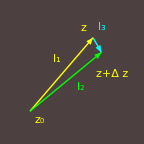
Δ F=F(z+Δ z)-F(z)
=∫_z_0^(z+Δ z) f(ξ)ⅆξ-∫_z_0^z f(ξ)ⅆξ
=∫_(l_1+l_3) f(ξ)ⅆξ-∫_l_1 f(ξ)ⅆξ
=∫_l_3 f(ξ)ⅆξ              -Graphics-

因为 f(z) 解析可导，必连续， ∀ε>0， ∃δ(ε)， 使得当  |ξ-z|<δ 时， |f(z)-f(ξ)|<ε，

求导时 Δ z→0， 故可取 |Δ z|<δ，那么在  l_3 上， |f(z)-f(ξ)|<ε，

|(F(z+Δ z)-F(z))/(Δ z)-f(z)|=|1/(Δ z)∫_l_3 f(ξ)ⅆξ-f(z)|   （无论 Δz 以何种方式→0，积分均可沿直线进行，因为与路径无关）

=|1/(Δ z)∫_l_3 [f(ξ)-f(z)]ⅆξ|≤ |1/(Δ z)|∫_l_3 |f(ξ)-f(z)|  |ⅆξ|

≤ 1/(|Δ z|) ε∫_l_3 |ⅆξ|= ε/(|Δ z|)|Δ z|=ε

由于 ε 可以任意小   ⟹    F'(z)=lim_(Δ z→0) (F(z+Δ z)-F(z))/(Δ z)=f(z)         F(z) 可导 ⟹  解析

F'(z)=f(z)，故 F(z)称为 f(z)的原函数。

类似于实变函数，下面证 f(z)的原函数之间只差一个常数。

设 F(z)和 G(z) 都是 f(z)的原函数，则：G'(z)=F'(z)=f(z)，

令： G(z)-F(z)=h(z) ,      h'(z)=G'(z)-F'(z)=0

h(z)=u+ⅈ v , h'(z) =u_x+ⅈ v_x=-ⅈ u_y+v_y=0     ⟹         u_x=u_y=v_x=v_y=0      ⟹    h(z) =常数。

（实际上，因为 F(z)和 G(z)解析，故 h(z)解析，又 h'(z)=0   ⟹^(作业 1.7(1))   h(z) =常数）

即： G(z)-F(z)=c，    F(z)=G(z)-c

以 z_0 代入上式：c=G(z_0)-F(z_0)=G(z_0)-(∫_z_0^z_0 f(ξ)ⅆξ)^(⏞^0)=G(z_0)      ⟹    G(z_0)=c

⟹ G(z)-G(z_0)=G(z)-c=F(z)= (∫_z_0_^(z^))^f(ξ)ⅆξ=F(z)-F(z_0)    ——  类牛顿莱布尼兹公式

这里利用了  F(z_0)=0

f(z) 的所有原函数的集合称为 f(z)的不定积分。注意只有解析函数 f(z) （在解析区域）才可以求不定积分。

### 复连通的Cauchy定理

定理： f(z) 在闭复连通区域 D̄内解析，则 f(z)沿所有内外边界线正向积分和为 0。

∳f(z)ⅆz=∳_L_0 f(z)ⅆz+(∑_(k=1))^n ∳_L_k f(z)ⅆz=0

证明：如下图作割线，变为单连通，如下左图图绕行即可。

-Graphics-          -Graphics-

推论一： 闭复连通区域 D̄内的单值解析函数，沿外境线逆时针走向的积分等于沿所有内镜线逆时针走向积分和。

推论二：在 f(z)的解析区域中，积分回路连续变形，积分值不变。

例：若 f(z) 在右图 L_0 与 L'_0 围成的复连通区域解析，

则沿蓝色 L_1 与 红色 L'_1 两条路径的积分相等，但不等于绿色路径 L''_1 的积分。

例题：求积分  I_n=∳_C (z-a)^n ⅆz， n  为整数，C 为包围 a 点的任意一条闭合回路正向（逆时针）。

n≥0    时，被积函数是解析函数， I_n=0；

n<-1 时，利用推论二，把 C 连续变形为圆心于 a，半径为 ε 的圆周

在 C 上：z=a+ε ⅇ^(ⅈ θ)   ⟹   ⅆz=ε ⅈ ⅇ^(ⅈ θ)ⅆθ    ⟹  I_n=∳_C (z-a)^n ⅆz=∫_0^(2π) ε^n ⅇ^(ⅈ n θ)  ε ⅈ ⅇ^(ⅈ θ)ⅆθ

I_n= ⅈ ε^(n+1)∫_0^(2π) ⅇ^(ⅈ (n+1)θ)ⅆθ=[ε^(n+1)/(n+1)ⅇ^(ⅈ(n+1)θ)]_0^(2π)=0            （这里利用了 n≠-1）

n=-1 时，仍然把 C 变形为圆心于 a，半径为 ε 的圆周

I_n=∳_C ⅆz/(z-a)=∫_0^(2π) (ε ⅈ ⅇ^(ⅈ θ))/(ε ⅇ^(ⅈ  θ))ⅆθ =2π ⅈ

综合：I_n=∳_C (z-a)^n ⅆz=2π ⅈ δ_(n,-1),       δ_(i j) ={1 |       if  i=j
0 |       if   i≠j      ——  Kronecker  delta 符号

例题：求积分  I_n=∫_C (z-a)^n ⅆz， C 为从 b_1 到 b_2 的一条路径，如左图。

选取一解析区域，如下右图黄色闭合回路围成的区域，在此解析区域里，积分可利用原函数概念。

n≠-1 时

沿如下左图绿色路径（沿紫色路径积分相同吗？）

I_n=∫_b_1^b_2 (z-a)^n ⅆz=[(z-a)^(n+1)/(n+1)]_b_1^b_2=((b_2-a)^(n+1)-(b_1-a)^(n+1))/(n+1)

-Graphics--Graphics-

n=-1 时

(I_-1=∫_b_1^b_2 1/(z-a)ⅆz=Ln (z-a)|)_b_1^b_2， 
这里利用了实变函数的积分公式：(ln z)'=1/z
但    Ln z 是多值函数，多值性来自 (z-a) 的辐角。
Ln(b_2-a)=ln|b_2-a| + ⅈ arg (b_2-a)+ⅈ 2k π  值不确定
故：积分与路径有关，或者说，积分值由路径确定。
如图积分从 b_1 沿绿线到达 b_2，arg(z-a)顺时针转过  Δθ
因此：I_-1=ln|(b_2-a)/(b_1-a)|- ⅈ Δθ   -Graphics-

为简单起见，取 a = 0，b_1=-2ⅈ，b_2=3i， C_1 从 b_1 跨过负实轴到达 b_2， C_2 从 b_1 跨过正实轴到达 b_2。

沿 C_1： z-a  矢量，顺时针转了  π，
即：Δarg (z-a) =-π, I_-1=∫_(-2ⅈ)^(3ⅈ) 1/z ⅆz=(ln 3/2)_(⏟_单值)+ⅈ (- π)
沿 C_2：z-a  矢量，逆时针转了  π，
Δarg z =π，I_-1=∫_(-2ⅈ)^(3ⅈ) 1/z ⅆz=ln 3/2+ⅈ π，
二者之差为：∫_C_2 +∫_((C̄)_1)=∫_C_2 -∫_C_1= 2π ⅈ=∳_C 1/z ⅆz，
其中 (C̄)_1 为 沿 C_1 逆向的积分。结果同上一例题。  -Graphics-

不妨设积分路径为： b_1 经圆心于原点半径为 2 的圆周到达 b'_1=2ⅈ，再沿虚轴到 b_2=3ⅈ，以验证。

结论：

∫_b_1^b_2 1/(z-a)ⅆz=ln(|b_2-a|)/(|b_1-a|)+ⅈ Δθ

其中  Δθ 为由积分路径确定的、复变量 (z-a) 转过的角度（逆时针为正顺时针为负）。

利用程序找点感觉： code02 .04 ContourIntegration.nb

例题：求积分  I=∫_0^ⅈ z/(z+1)ⅆz， 积分路径为从原点出发进入第一象限，而后到达 z=ⅈ

解：被积函数在右半平面是单值解析函数

可用类牛顿莱布尼兹公式。
I=∫_0^ⅈ z/(z+1)ⅆz
   =∫_0^ⅈ ⅆz-∫_0^ⅈ 1/(z+1)ⅆz
(=ⅈ-Ln^ (z+1)|)_0^(ⅈ^)
   =ⅈ -[ln √2+ⅈ (θ_2-θ_1)]
    =ⅈ-ln √2-ⅈ π/4               -Graphics-

其中 (θ_2-θ_1)是 z+1 矢量从 z=0 到 z=ⅈ 所转过的角度，如图所示。沿 C 与 C'，积分相同。

例题：求积分  I=∫_-a^a ⅆz/(z^2+1)， 积分路径为沿|z|=a 的上半圆周从 z=-a 到 z=a

提示：arctan z=1/(2ⅈ)ln ((1+ⅈ z)/(1-ⅈ z))

解：记得：(arctan x)'=1/(1+x^2),    以下假设 a<1。把 a>1情况留作练习。

((I=1^□arctan z |)_-a^a=1/(2ⅈ)ln ((1+ⅈ z)/(1-ⅈ z))|)_-a^a
(=1/(2ⅈ)ln ((ⅈ-z)/(ⅈ+z))|)_-a^a
=1/(2ⅈ) [ ln|(ⅈ-a)/(ⅈ+a)|-ln|(ⅈ-(-a))/(ⅈ+(-a))| ]^(⏞^(= 0))
(+1/(2ⅈ)[ⅈ arg (ⅈ-z)-ⅈ arg(ⅈ+z)]|)_-a^a
((=1/2 arg (ⅈ-z)|)_-a^a-1/2 arg(ⅈ+z)|)_-a^a
=1/2(2θ)-1/2(-2θ)
=2θ=2 arctan a         -Graphics-

(其中：■_□^□arg (ⅈ-z)|)_-a^a   表示 ⅈ-z 矢量在 z 沿积分路径从 z=-a 到 z=a 扫过的角度，逆时针为正

(■_□^□arg (ⅈ+z)|)_-a^a   表示 z-(-ⅈ) 矢量在 z 沿积分路径从 z=-a 到 z=a 扫过的角度，顺时针为负

注意：  ⅈ-z 为从 z 到 ⅈ 的矢量，z-(-ⅈ) 为从 -ⅈ 到 z 的矢量

本题目的在于利用：arctan z 是 1/(1+z^2)的“原函数”。更简单地，本题可化为：

(I=1/(2ⅈ)∫_-a^a (1/(z-ⅈ)-1/(z+ⅈ))ⅆz=1/(2ⅈ)[ Ln(z-ⅈ)-Ln(z+ⅈ)]|)_-a^a  ，继而关注 z±ⅈ 的辐角变化。试验证最终结果相同。

### 小圆弧引理与大圆弧引理

小圆弧引理：若 f(z) 在 z=a 的去心邻域内连续，在一段小圆弧 C_r： z-a=r ⅇ^(ⅈ θ)， θ_1≤ arg (z-a) =θ≤θ_2 上

lim_(r→0) (z-a)f(z)=k    一致成立，则

lim_(r→0) ∫_C_r f(z)ⅆz=ⅈ k (θ_2-θ_1)

说明：一致成立表明，对 ∀ε>0，在 z 的辐角 θ 满足 θ_1≤ θ≤θ_2 时，存在与 θ 无关的 δ，

使得当 |z-a|<δ 时，|(z-a)f(z)-k|<ε。

证明：证明积分等于某个值，常化为证明积分为 0 形式，即：需要证明 r→0 时，

I=∫_C_r f(z)ⅆz-ⅈ k(θ_2-θ_1)=0，在 C_r 上:  ∫_C_r ⅆz/(z-a)=∫_θ_1^θ_2 (r ⅇ^(ⅈ θ)ⅈⅆθ)/(r ⅇ^(ⅈ θ))=ⅈ (θ_2-θ_1)

ⅈ k(θ_2-θ_1) =∫_C_r kⅆz/(z-a)   与  ∫_C_r f(z)ⅆz 凑成单一个积分形式：∫_C_r (f(z)-k/(z-a))ⅆz

I=∫_C_r (f(z)-k/(z-a))ⅆz=∫_C_r ((z-a)f(z)-k)/(z-a)ⅆz，需要证明 r→0时此积分为 0

要证明积分为 0，常用积分的绝对值总小于先取绝对值在积分。在 C_r 上，z=a+r ⅇ^(ⅈ θ), ⅆz=ⅈ r ⅇ^(ⅈ θ)ⅆθ

|I|≤∫_C_r (|(z-a)f(z)-k|)/(|z-a|)|ⅆz|≤^(1)ε∫_C_r (|ⅆz|)/(|z-a|)=ε∫_C_r rⅆθ/r=ε (θ_2-θ_1)，小于任意小的正数

注 (1)：这里利用了 |(z-a)f(z)-k|<ε，故要求lim_(r→0) (z-a)f(z)=k 在积分路线上一致成立。

即：∀ ε>0，∃ δ （这个 δ 与积分变量 z 在 积分路线 C_r 上的取值无关），

使得只要 θ_1≤ θ≤θ_2 且|z-a|<δ，必有|(z-a)f(z)-k|<ε。

这样才能保证只要 r 足够小（r<δ），只要 z 在积分路线 C_r 上，

都有 |(z-a)f(z)-k|<ε，从而 ε 可拿出积分号之外。这就是“一致”的效应。

大圆弧引理：若 f(z) 在无穷远点的去心邻域内连续，在一段大圆弧 C_R： z = R ⅇ^(ⅈ θ),  R→∞,  θ_1≤ θ≤θ_2 上

lim_(R→∞) z f(z)=K     一致成立，则

lim_(R→∞) ∫_C_R f(z)ⅆz=ⅈ K (θ_2-θ_1)           注意 K=0 即为上一节的例题

证明：需要证明在 R→∞ 时，

I=∫_C_R f(z)ⅆz-(ⅈ K (θ_2-θ_1))^(⏞^也化成积分形式)=0，在 C_R 上:  ∫_C_R ⅆz/z=∫_θ_1^θ_2 (R ⅇ^(ⅈ θ)ⅈⅆθ)/(R ⅇ^(ⅈ θ))=ⅈ(θ_2-θ_1)

I=∫_C_R (f(z)-K/z)ⅆz=∫_C_R ((z f(z)-K)^(⏞^凑成这个形式))/z ⅆz，

写成 z f(z)-K 形式，即可利用 lim_(R→∞) z f(z)=K，即：|z f(z)-K|<ε

|I|≤∫_C_R (|z f(z)-K|)/(|z|)|ⅆz|≤ε∫_C_R (|ⅆz|)/(|z|)=ε (θ_2-θ_1)         这几步与小圆弧引理的证明类似

大圆弧与小圆弧定理今后常用，如何理解？

问题都归结为：计算一段圆弧上的积分：∫_C f(z)ⅆz

如果是小圆弧 C_r（圆心于 z=a, 半径 r→0）,积分弧长 ∼ r  趋于 0，若 f(z) 有界，则积分为 0，因此仅当 f(z) 趋于无穷时，积分才不为 0。

但 f(z) 也不能是“高阶无穷”，应该是 ~1/r，因此仅在 lim_(r→0) (z-a)^(⏞^((z-a) ∼ r))f(z)有限时积分才给出有限值。

如果是大圆弧 C_R（半径 R→∞）,积分弧长 ∼ R 趋于 ∞，对任意有限张角的积分，仅当 lim_(R→∞) f(z)趋于 0， 积分才不发散。

因为积分弧长正比于 R，因而 f(z) ∼ 1/R∼ z，故要在 lim_(R→∞) z f(z)有限时，也即弧长与函数值的乘积有限时，积分值才是有限值。

## 2.2 Cauchy 公式及其推论

解析函数不是随便两个二元实变函数的组合，而是由两个满足调和性的相互间存在共轭关系（C-R条件）的二元实变函数有序构成，知其一必知其二。

此外，解析函数还有另一个特殊性质：解析函数各点的函数值不相互独立，特别是，给定边界上的值，则内部各点的值就确定。

这就是本节要讨论的 Cauchy 公式：由边界值确定内部任一点的函数值。实变函数无此特性。

在电磁理论中，若知道边界上电磁场的值，即可知道内部电磁场。

目前能容易求出的积分

1.     I_n=∳_C (z-a)^n ⅆz=2π ⅈ δ_(n,-1)

2.    对解析函数 f(z):    ∮_C f(z)ⅆz=0         （Cauchy 定理）

3.    能简单地求出原函数的解析函数的积分（特别适合非闭合路径）

4.    若干定理：大圆弧定理，小圆弧定理，约当引理等。

要计算诸如∳_C ⅆz/(z sin z) 的积分（C 包围了 z=0点），还需要更多的定理、公式。

### 有界单连通区域的Cauchy公式

设函数 f(z) 在闭单连通区域 D̄上解析， C为区域边界（分段光滑），则区域内任意一点 a 的函数值

f(a)=1/(2π ⅈ)∳_C (f(z)ⅆz)/(z-a)，       区域内部的函数值由边界的函数值完全确定

∳_C   表示积分路径沿边界 C 的正向 （外边界是逆时针方向）

证明：因为函数 f(z) 解析，积分回路可连续变形至 C_r： z=a+r ⅇ^(ⅈ θ),   r→0   （圆心于 a 半径为 r 的圆周）

令：g(z)=(f(z))/(z-a) ，  需要计算一段圆弧上的积分：∳_C_r g(z)ⅆz      ——  小圆弧定理

lim_(r→0) (z-a)g(z)=  lim_(r→0) f(z)=f(a)=k

可对 g(z)应用小圆弧引理   ⟹   ∳_C_r g(z)ⅆz=ⅈ 2π f(a)

Cauchy 公式成立的条件：

在以 C 为边界的单连通闭区域 D̄ 内f(z) 解析；可推广为开区域 D 内解析，边界线 C 连续

点 a 在区域 D 内（是内点，不能是边界点）。

注：以下积分例题用以后的留数定理计算更为简便，在此仅用于帮助理解 Cauchy 公式

例题

I=∳_C ⅇ^z/(z^2+1)ⅆz,    C 为  |z+ⅈ|=1 的圆

奇点：z=±ⅈ,     I=∳_C (ⅇ^z/(z-ⅈ))/(z+ⅈ)ⅆz

f(z)=ⅇ^z/(z-ⅈ)   在 C 围成的单连通闭区域解析

I=2π ⅈ f(-ⅈ)=-π ⅇ^-ⅈ

例题

I=∳_C 1/(z^4+1)ⅆz,    C 为  x^2+y^2=2x  的圆

奇点：f(z)=z^4+1 的4个根，z_k=ⅇ^(ⅈ π/4 + ⅈ k π/2), k=0,1,2,3

-Graphics-

C 包围了两个奇点，构成复连通解析区域

复连通 Cauchy 定理的推论：沿外境线逆时针走向的积分等于沿所有内镜线逆时针走向积分和。

I 化成沿 c_1 和 c_4 的积分

f(z)=1/(z^4+1)=1/((z-z_1)(z-z_2)(z-z_3)(z-z_4))

I_1=∳_c_1 f(z)ⅆz=∳_c_1 (f_1(z))/(z-z_1)ⅆz,    把 f(z)在 c_1 内的非解析点 a 写成 1/(z-a)形式，剩余部分构成解析函数

f_1(z)=1/((z-z_2)(z-z_3)(z-z_4))在 c_1 围成的区域内解析，可应用 Cauchy 公式

I_1=2π ⅈ f_1(z_1)，   I=2π ⅈ [f_1(z_1)+f_4(z_4)]=-ⅈ π/√2

其中   f_4(z)=1/((z-z_1)(z-z_2)(z-z_3))。

例题表明，可利用Cauchy公式把被积函数在奇点 z_0 的非解析行为归结为 1/(z-z_0)，解析部分凑成分子

如果归结不成  1/(z-z_0)形式，例如：(cos z)/(z-z_0)^3，Cauchy 公式无能为力，要用“高阶导数的Cauchy公式”

### 有界复连通区域的Cauchy公式

设函数 f(z) 在闭复连通区域 D̄上解析， C为区域所有边界的正向，则区域内任意一内点 a 的函数值

f(a)=1/(2π ⅈ)∳_C (f(z)ⅆz)/(z-a)，           C=L_0+∑_k L_k   为所有边界的正向（外境线逆时针，内境线顺时针）

证明：作割线，视为单连通区域即得。

-Graphics-

推论，对解析函数 f(z)

1/(2π ⅈ)∳_C (f(z)ⅆz)/(z-a)=Piecewise[{{f(a), 对 a 点在回路 C 之内}, {0, 对 a 点在回路 C 之外}}]              a 在回路上？积分路线上出现奇点 —— 反常积分

单、复连通区域的Cauchy公式，均要求 f(z) 在一个闭区域解析，C 为区域所有边界的正向。

而函数 f(z) 在一个闭区域 D̄ 上解析的定义为：可找到一个包含该闭区域的开区域 E， f(z) 在 E 上解析。

### 无界区域的Cauchy公式

设函数 f(z) 在闭回路 L 及 L 的外部解析， 且 lim_(z→∞) f(z)=0 (一致趋于 0），则对 L外任意一点 a

f(a)=1/(2π ⅈ)∲_(C^-) (f(z)ⅆz)/(z-a)，   C^- 为 L 顺时针（仍为边界正向，只不过这时是内边界，顺时针）

-Graphics-

证明：以 z=0 为中心，做一大圆 C_R 使得 a 和 L 均在 C_R 之内

由复连通区域的Cauchy公式

f(a)=1/(2π ⅈ)∲_(C^-) (f(z)ⅆz)/(z-a)+1/(2π ⅈ)∳_C_R (f(z)ⅆz)/(z-a)     （注意两个积分号的差异：∲  vs  ∳）

第一项为所求证的，故需要证明第二项为 0。可作如下分析：

R→∞ 时，f(z)→0,  弧长  ⅆz ~ R，而 1/(z-a)~ 1/R，故第二项应该→0

这种情况的严格证明，可利用大圆弧引理。以下证明之。

g(z)=(f(z))/(z-a),        z g(z)=(z f(z))/(z-a),

lim_(z→∞) z g(z)=lim_(z→∞) (f(z))/(1-a/z)=lim_(z→∞) f(z)=K=0

利用大圆弧引理：∳_C_R (f(z)ⅆz)/(z-a)=∳_C_R g(z)ⅆz=ⅈ 2π K=0

f(a)=1/(2π ⅈ)∲_(C^-) (f(z)ⅆz)/(z-a)

若函数 f(z) 在闭回路 L及 L外部解析， 且 lim_(z→∞) f(z)=A，则  （试证之）利用  ∲_(C^-) + ∲_C_R ={2π ⅈ f(z)
0  和  ∲_C_R =2π ⅈ A

1/(2π ⅈ)∲_(C^-) (f(ζ))/(ζ-z)ⅆζ={ f(z)-A |        z 在回路之外
-A |                    z 在回路之内，  C^- 为 L 顺时针（仍为边界正向）

### Cauchy公式的推论

解析函数的高阶导数（高阶导数的Cauchy公式）

设 f(z) 在闭区域 Ḡ（可能是复连通区域）内解析，则在 G内， f(z) 可以有任意阶导数，且

f^(n)(z)=(n!)/(2π ⅈ)∳_L (f(ξ))/(ξ-z)^(n+1)ⅆξ,            L 为 Ḡ 的所有边界的正向。

证明：利用数学归纳法。

n=1 时：

f'(z)=lim_(h→0) (f(z+h)-f(z))/h ⟹^利用Cauchy公式  f'(z)=lim_(h→0) 1/(2π ⅈ h)∳_L [(f(ξ))/(ξ-z-h)-(f(ξ))/(ξ-z)]ⅆξ

=  lim_(h→0) 1/(2π ⅈ)∳_L (f(ξ)  ⅆξ)/((ξ-z-h)(ξ-z))     ⟹^是否等于       1/(2π ⅈ)∳_L (f(ξ)  ⅆξ)/(ξ-z)^2

还是把等式写成较熟悉的某个积分  I=0 的形式，设二者之差为 I

I=1/(2π ⅈ)∳_L (f(ξ))/(ξ-z)[1/(ξ-z-h)-   1/(ξ-z)]ⅆξ,    要证明 I=0，利用惯用伎俩，取绝对值

|I|≤ (|h|)/(2π)∳_L (|f(ξ)|)/(|ξ-z|)^2(|ⅆξ|)/(|ξ-z-h|)，

注意 ：h→0，故应看被积函数的每一项是否有界，边界长度是否有限

a)  f(z)在闭区域 Ḡ 内解析，故 |f(ξ)|在边界 L 上必然有界，|f(ξ)|<M_1

b)  z 为区域 G 内确定（不随 h 改变）的内点，ξ 在边界 L 上，(z-ξ)≠0  ⟹   1/(|ξ-z|)^2 <M_2   有界

c)  因为 h→0，故  z+h 也不在边界 L 上    ⟹  1/(|ξ-(z+h)|) <M_3   有界

故：|I|< (|h|)/(2π) M_1 M_2 M_3 l,   l  为边界 L 的长度。

|I| < |h| M,   其中 M 有界     ⟹       lim_(h→0) I =0

n=1情况得证。

n≥2 时，用数学归纳法证明。

高阶导数Cauchy公式表明，一个复变函数，只要在某闭区域存在一阶导数，则存在任意阶导数。

或者说：一个复变函数只要在某个区域解析，则它必有任意阶导数。

只要解析，由高阶导数的Cauchy公式知， f'(z) 也解析，但 f'(z)=u_x+ⅈ v_x=-ⅈ u_y+v_y

⟹  四个偏导数必然连续，

故：只要解析，则任意阶导函数也解析，从而四个偏导数必存在且连续。

区域解析、Cauchy 定理、Cauchy 公式、任意阶导数之间的关系

（C-R条件）+（u, v 连续）⟺^充要条件  解析  (⟹^四偏导数连续)_格林公式   Cauchy定理

⟹^  Cauchy公式     ⟹^  任意阶导数 f^(n)(z)   ⟹^  四偏导数连续

循环论证？Goursat 在不利用四偏导数连续的条件下证明了Cauchy定理。

参阅：ref02.01 柯西定理的古莎证明.pdf  或  Ahlfors “Complex Analysis”

复变函数在闭区域 Ḡ 解析，则有任意阶导数，实变函数则不然。

f(x)=Piecewise[{{x^2 sin 1/x, x≠0}, {0, x=0}}],

在闭区间 |x|≤1 存在一阶导数，但二阶导数不存在。

在复数域，若在闭某区域一阶导数存在，则任意阶导数存在。

退回作为复数子集的实数域，为何一阶导数存在，二阶导数反而可能不存在？

换句话说，以下命题，对实数域不成立，对复数域成立

“一个函数若在某闭区域 Ḡ 存在一阶导数，则在该区域，任意阶导数均存在”

佯谬？在一个子集里都不成立的命题（若一阶可导则任意阶可导），在更大的数集反而成立？

实际上，把上述函数定义到复数域，就会发现 f'(z) 在 z=0  点不存在。

换言之：对复变函数，解析的要求是如此严格，以至于一旦满足一阶导数存在，则任意阶导数也都存在。

对实变函数，因可导的要求较低，未免滥竽充数鱼目混珠者，经不起多阶求导的考验。

例题      若能把被积函数在奇点 z_0的非解析行为表为 1/(z-z_0)^(n+1)，则高阶导数的Cauchy公式即可用于求积分

I=∳_C ⅆz/(z sinz),    C 为  |z|=1 的圆周

I=∳_C (z/sin z)/z^2 ⅆz,    f(z)=Piecewise[{{z/sinz, z≠0}, {1, z=0}}] 在区域内解析

I=∳_C (z/sin z)/z^2 ⅆz=(2π ⅈ)/(1!)f'(0)=2π ⅈ (sin z-z cos z)/(sin^2 z)=0

其中用到了洛必达法则

### Morera定理 —— Cauchy定理的逆定理

如果 f(z) 在闭区域 Ḡ中连续，且对  Ḡ 内的任意一闭合回路 L 都有

∳_L f(z)ⅆz=0,  则 f(z) 在 G 内解析。

证明：任意闭合回路积分为 0，故对任意 z∈G

F(z)=∫_z_0^z f(z)ⅆz 与路径无关，故 F(z)为单值函数，以下证明： F'(z)=f(z)

|(F(z+h)-F(z))/h-f(z)|=1/(|h|)|∫_z^(z+h) [f(ξ)-f(z)]ⅆξ|≤ 1/(|h|)∫_z^(z+h) |f(ξ)-f(z)||ⅆξ|≤1/(|h|)ε |h|

即：F'(z)=f(z)，故 F(z) 在 G 内解析，由高阶导数的Cauchy公式知，F'(z) =f(z)也必然解析。

例题：若 F(z) 在区域 G 内解析，f (z) ≡{(F(z)-F(z_0))/(z-z_0), |  z≠z_0
F'(z_0), | z=z_0 ，试证明f(z) 也在区域 G 内解析

证明：f(z)貌似 F'(z)，实际上它仅在 z=z_0 点才为 F'(z_0)，

故不宜用：若 F(z)解析则 F'(z)解析来证明 f(z)解析。

关键在 z=z_0 点，因为对 z≠z_0，F(z)-F(z_0) 与 z-z_0 都解析，

利用解析函数的商也解析（只要分母不为 0），故 f(z)在 z≠z_0 点是解析的。

如何证明在 z=z_0 点 f(z) 解析？利用 Morera 定理。

考虑以 z_0 为圆心，ε 为半径的小闭区域 D̄(z_0,ε)，证明在 D̄(z_0,ε)内解析。

显然 f(z) 在 D̄ 内连续，闭区域连续必为一致连续且有界：|f(z)|<M

下证明 I=∳_C f(z)ⅆz=0，   C 为 D̄ 内的任意一闭合回路。

若回路 C 不包围 z_0，则 C 包围一解析区，I=0
若回路 C 包围 z_0，则 C 可以变形为一个圆心在 z_0 半径为 δ 的圆 C_δ，
            I=∳_C_δ f(z)ⅆz       证明积分 I 为 0，老方法
            |I|≤   ∳_C_δ |f(z)||ⅆz|<M ∳_C_δ |ⅆz|=M 2π δ,    δ→0, 故 I=0
若回路 C 经过 z_0，把 C 变形绕过 z_0 点，如图从 A 经 z'_0 到 B
          由于 f(z) 一致连续，从 A 经 z'_0 到 B 与 从 A 经 z_0 到 B 的积分相同  -Graphics-

故积分 I 仍为 0

综上：  f(z)连续且∳_C f(z)ⅆz=0，由 Morera 定理，f(z)解析。

当然，本题主要用于理解 Morera 定理和一致连续在积分中的作用，

实际上，也可直接证明 f(z) 在 z_0 点可导。可以证明： f'(z_0)=F''(z_0)，即 f(z)在 z_0 可导。

### Cauchy不等式

如 f(z) 在闭区域 Ḡ上解析，则

|f^(n)(z)|≤ (n!)/(2π)(M l)/d^(n+1)

M 为 |f(z)| 在闭区域 Ḡ上的最大值， l 为边界长度， d 为 z 到边界的最短距离

证明：这是高阶导数的Cauchy公式的直接推论。

f^(n)(z)=(n!)/(2π ⅈ)∳_L (f(ξ))/(ξ-z)^(n+1)ⅆξ

### 均值定理

定理：f(z) 在解析区内任意一点 a 的函数值 f(a)，等于以 a为圆心，完全于解析区的任意一个圆周上的函数值的平均。

f(a)=1/(2π)∫_0^(2π) f(a+r ⅇ^(ⅈ θ))ⅆθ

证明：由Cauchy公式

f(a)=1/(2π ⅈ)∳(f(z))/(z-a)ⅆz,   令  z=a+r ⅇ^(ⅈ θ), 代入即得。

### 最大模、最小模定理

定理：f(z) 在闭区域 Ḡ上解析，则 |f(z)| 只能在 Ḡ 的边界上取最大值。

也即解析函数在开区域 G 内，|f(z)| 最多只有鞍点。

证明：由Cauchy不等式，若  |f(z)|  在边界上的最大值为M，则

|f(z)|≤ 1/(2π)(M l)/d     并令：g(z)=[f(z)]^n    ⟹  f(z) 解析，g(z) 也解析

∀z∈G,    (|f(z)|)^n=|[f(z)]^n|=|g(z)|=|1/(2π ⅈ)∳[f(ξ)]^n/(ξ-z)ⅆξ|≤ 1/(2π)(M^n l)/d

|f(z)|≤ (M(l/(2π d)))^(1/n),  令 n→∞ 即得

|f(z)|≤ M

以上证明并不严格，漏洞在哪儿？请思考。因为f(z) 解析，并不意味着 [f(z)]^n 在 n→∞ 时也解析。

严格的证明

若 |f(z)| 存在内点最大值，这个最大值必为|f(z)|的极大值 
故若 |f(z)| 在某一内点 z_0 取最大值，则必可找到一个 δ 邻域 C_δ ，
 |z-z_0|≤δ （如图绿色圆所示），∀z∈C_δ, 有 |f(z)|≤|f(z_0)|
取 C_ε 为|z- z_0|=  ε≤ δ ，如图黄色圆所示，Cauchy公式，有
|f(z_0)|=|1/(2π ⅈ)∳_C_ε (f(z))/(z-z_0)ⅆz|≤1/(2π)∳_C_ε (|f(z)|)/(|z-z_0|)|ⅆz|
|f(z_0)|≤1/(2π)∫_0^(2π) |f(z_0+ε ⅇ^(ⅈ θ))|ⅆθ
上式左边|f(z_0)| 为|f(z)|在区域 C_δ 里的极大值，
上式右边为|f(z)|在圆周 C_ε 上的平均值，故该式表明：
                    对圆周 C_ε 上的点 z_ε，|f(z_ε)|=|f(z_0)|。     -Graphics-

而圆周半径  ε 可在0<ε≤δ 间变化，故|f(z)|在整个 δ 邻域 C_δ 内均等于 |f(z_0)|。

对 C_δ 边界上的点 z_δ，|f(z_δ)|=|f(z_0)|。即，|f(z)| 在 C_δ 的边界点 z_δ 取最大值。

对 C_δ 的边界点 z_δ 再次应用上述讨论，可导出：在整个闭区域 Ḡ 上，均有|f(z)|=|f(z_0)|。

这就是说，一旦 |f(z)| 在某一内点 z_0 取最大值 |f(z_0)|，则整个闭区域上， |f(z)| =|f(z_0)|=常数。

在某解析区，若 |f(z)| =常数，则 f(z)=常数，参见作业1.7(4)。

更简明的证明参见 “§3.3 解析函数的Taylor展开”一节的例题。

一般在G 内，|f(z)|<M，仅当  |f(z)|≡M 时等号才成立，而 |f(z)|≡M 意味着 f(z)=c ，见作业1 .7(4)，故仅当 f(z)=c 时等号才成立。

如在 Ḡ 内 f(z)≠0，则 g(z)=1/(f(z)) 也在 Ḡ内解析， |g(z)| 只能在边界上取最大值， 对应地，|f(z)| 只能在边界上取最小值。

Earnshaw（恩紹）定理：仅靠静电力无法使得点电荷体系获得力学平衡。（静磁也类似）

数学理解：电势能用解析函数描述，极值点在边界。
磁悬浮玩具，不可能达到静态平衡，但可以动态平衡（自转的地球）
YANGHX Levitation Floating Globe      amazon.com

### Liouville定理

定理：若函数 f(z) 在整个复平面（不包括无穷远点）上解析，且当 z→∞ 时  |f(z)| 有界，则 f(z)=c。

证明：利用一阶导数的 Cauchy 公式

f'(z)=1/(2π ⅈ)∳_C_R (f(ξ))/(ξ-z)^2 ⅆξ,   当 R→ ∞ 时，|f(z)|<M,

|f'(z)|≤ 1/(2π)∳_C_R (|f(ξ)|)/(|ξ-z|)^2|ⅆξ|≤ M/(2π)(2π R)/d^2

d 为大圆周到到 z 点的最近距离  d~R

故取积分圆半径 R→ ∞, |f'(z)|=0

|f'(z)|=0    ⟹   f'(z)=0    ⟹^(习题1.7(1))   f(z)=c

在整个实轴(-∞,+∞)上可微且有界的实变函数未必是常数，如 cos x, sin x，

在整个复平面上可微且有界的复变函数必然是常数。

在整个复平面上解析的函数称为整函数，故 Liouville 定理表明：有界的整函数必为常数。

若 f(z)  是整函数，并且 |f(z)|≥c>0，则f(z) 是一常数。

这个性质表明：无零点的整函数也为常数，以后我们还将证明，解析函数的零点是孤立的。

证明：令 g(z)=1/(f(z))，显然，g(z)是有界的整函数，是常数，从而 f(z)也为常数

例题：试证明复系数 n 次多项式在复平面内有 n 个根。

说明：本课程在引进复数时曾经戏说：引进复数的动机之一可理解为：使得 n 次多项式有 n 个根。

当时没有证明，现在补补妆，系系鞋带：“当窗理云鬓，对镜贴花黄”。

证明：不失一般性，我们将 n 次多项式写成：

p_n(z)=z^n+a_(n-1)z^(n-1)+a_(n-2)z^(n-2)+…+a_1 z+a_0      （z^n 的系数不为 0，故可归一化为 1）

我们先证明：p_n(z) 在复平面内至少有一个根（这个性质称为代数学基本定理），

接着，把 p_n(z) 化为 n-1 次多项式 p_(n-1)(z) ，以此类推，直到 p_1(z)。

为证明p_n(z) 有一个根，利用反证法。

假设 p_n(z)在整个复平面没有根，即：对任何有限的 z，p_n(z)≠0

既然 p_n(z)≠0,  g_n(z)= 1/(p_n(z)) 就在全平面解析——整函数

原因是：因为若两函数均在D内解析，则其和、差、积、商（分母不为 0）也在D内解析。

接着，再证明g_n(z) 有界

lim_(z→∞) g_n(z)=lim_(z→∞) 1/z^n 1/(1+(a_(n-1))/z+…+a_1/z^(n-1)+a_0/z^n)
=lim_(z→∞) 1/z^n lim_(z→∞) 1/(1+(a_(n-1))/z+…+a_1/z^(n-1)+a_0/z^n)=0          ⟹      lim_(z→∞) g_n(z)=0

既然 g_n(z)在全平面解析且 lim_(z→∞) g_n(z)=0，由 Liouville 定理： g_n(z)=c 常数，与 g_n(z)=1/(p_n(z)) 矛盾。

故：p_n(z) 在复平面内必有一根 z_1，p_n(z) 可表为：

p_n(z)=z^n+a_(n-1)z^(n-1)+a_(n-2)z^(n-2)+…+a_1 z+a_0 
⟹^(能否写成?)   (z-z_1)(z^(n-1)+b_(n-2)z^(n-2)+b_(n-3)z^(n-3)+…+b_1 z+b_0)

即，是否有：(z-z_1)(∑_(k=0))^(n-1)b_k z^k=(∑_(k=0))^n a_k z^k        其中：b_(n-1)=a_n=1

⟹     左=  (∑_(k=0))^(n-1)b_k z^(k+1)-(∑_(k=0))^(n-1)z_1 b_k z^k=b_(n-1)z^n-z_1 b_0+(∑_(k=1))^(n-1)(b_(k-1)-z_1 b_k)z^k

⟹     右=a_n z^n+a_0+ (∑_(k=1))^(n-1)a_k z^k,   注意：b_(n-1)=a_n=1

其中通过比较上式两边 z^k 的系数，k=0, 1, … n-1 ，

即可得 m 个线性方程：{b_(k-1)-z_1 b_k=a_k,   k=1,…,n-1
-b_0 z_1=a_0

从而求得：b_0, b_1, …, b_(n-3), b_(n-2) 这 n-1 个系数

从而：p_n(z)=(z-z_1)p_(n-1)(z),    其中 p_(n-1)(z) 为 n-1 次复系数多项式。

接下去，以此类推，即可得：复系数n 次多项式有 n 个根。

### Cauchy型积分

定理：在一段分段光滑的曲线 L上的连续函数 ϕ(ξ)所构成的积分

F(z)=1/(2π ⅈ)∫_L (ϕ(ξ))/(ξ-z)ⅆξ    （称为 Cauchy 型积分）

Cauchy 型积分对曲线 L 外的任意点 z 是解析函数。

证明：需证明 F'(z) 对曲线外的任意点 z 都存在。从导数的定义出发，

F'(z)=(F(z+h)-F(z))/h=1/h∫_L [(ϕ(ξ))/(ξ-z-h)-(ϕ(ξ))/(ξ-z)]ⅆξ

h→0，故总可以使 z+h 与 z 都不在曲线 L上

F'(z)=∫_L (ϕ(ξ)ⅆξ)/((ξ-z-h)(ξ-z)) =∫_L (ϕ(ξ)ⅆξ)/(ξ-z)^2

其中最后一步请同学参照本章高阶的导数Cauchy公式的证明自己完成。

既然 F(z) 解析，它必有高阶导数，还可证明：

F(z)=1/(2π ⅈ)∫_L (ϕ(ξ))/(ξ-z)ⅆξ        ⟹      F^(n)(z)=(n!)/(2π ⅈ)∫_L (ϕ(ξ)ⅆξ)/(ξ-z)^(n+1),    n=0,1,2,…

注意此式与高阶导数 Cauchy 公式之异同：f^(n)(z)=(n!)/(2π ⅈ)∳_L (f(ξ))/(ξ-z)^(n+1)ⅆξ

(1.EquationNumbered) 式的另一种理解是：Cauchy 型积分的求导与求积可交换次序：

F^(n)(z)=(n!)/(2π ⅈ)∫_L (ϕ(ξ)ⅆξ)/(ξ-z)^(n+1)

例题：若 f(z) 在闭区域 D̄ 上内是连续的，并且除 D̄ 内的一条直线段 l 上的点之外， f(z) 在 D̄ 内处处可导。试证明： f(z) 在 D̄ 内解析。

证明：条件：函数 f(z) 在闭区域 D̄ 内连续且除一条线段上的点不能保证可导外，其余的点均可导

需证：这条线段 l 上的点也都可导（解析）。

理解：如果在一区域内存在一些尚不能确定是否可导的点，若函数这些点上连续，则必可导。

若在一解析区域内存在一些不可导的点（奇点），则在函数这些点上必然不连续。

初等函数的奇点都是不连续点。注意：一般的函数可能存在连续但不可导的点。

在线段上任取一点 z_0，如图所示，
绿线为可能存在不可导点的线段，
               红闭合曲线是区域 D̄ 的边界
以 z_0 为圆心作圆，如图黄色线 L=L_1+ L_2
函数在闭区域内连续，必然有界且一致连续
设 L_1 与红色直线构成区域 D_1，其边界为 L'_1
      L_2  与紫色直线构成区域 D_2，其边界为 L'_2
 D_1 内任取一点 z，因为 D_1 内解析，D_1 边界连续
故有：{f(z)=1/(2π ⅈ)∳_L'_1 (f(ζ))/(ζ-z)ⅆζ
0=1/(2π ⅈ)∳_L'_2 (f(ζ))/(ζ-z)ⅆζ     -Graphics-

两式相加，并注意到红色直线与紫色直线积分相消

（注意，一致连续保证了红、紫直线积分相消，参见一致连续）

得：f(z)=1/(2π ⅈ)∳_(L_1+L_2) (f(ζ))/(ζ-z)ⅆζ =1/(2π ⅈ)∳_L (f(ζ))/(ζ-z)ⅆζ         注意 z 在封闭曲线 L 所围成的 D_1 内

现在让 z 趋于 z_0

首先，|f(ζ)|在 L 上存在最大值：M

其次 1/(ζ-z)作为 z 的函数是一致连续的，

即：对 ∀ε>0, ∃ δ （与 z 都无关的 δ），使得 |z-z_0|<δ 时，|1/(ζ-z)-1/(ζ-z_0)|<ε

故：Δ=|1/(2π ⅈ)∳_L (f(ζ))/(ζ-z)ⅆζ  -1/(2π ⅈ)∳_L (f(ζ))/(ζ-z_0)ⅆζ |  
=|1/(2π)∳_L f(ζ)(1/(ζ-z)-1/(ζ-z_0))ⅆζ |      记得 z→z_0，故  |z-z_0|<δ
≤ 1/(2π)M ε ∳_L |ⅆζ|=M ε r,     r 为 L 的半径

即：lim_(z→z_0) Δ =0    ⟹   f(z)在线段上的函数值可表为：

f(z_0)=1/(2π ⅈ)∳_L (f(ζ))/(ζ-z_0)ⅆζ       ——  Cauchy 型积分   ⟹    f(z) 在 D̄ 内解析。

另证：其实本题更简单地可以用Morera定理。证明 ∳_L f(z)ⅆz 对任意闭路均为 0。

在区域 D̄ 内任取一闭合回路 L，如图
a)若 L 不包含线段 l，如图 L_3（宝蓝色），
      因 f(z) 在 D̄ 内除 l 外处处可导（解析）
          自然有： ∳_L_3 f(z)ⅆz=0
b) 若 L 包含一段线段 l，如图 L_1+L_2 （黄色）
        可作 l_1^′ 与 l_2^′，有
         { ∳_(L_1+l_1^′) f(z)ⅆz=0
∳_(L_2+l_2^′) f(z)ⅆz=0  -Graphics-

可以证明：∫_(l_1^′) f(z)ⅆz=-∫_(l_2^′) f(z)ⅆz    （见下）    ⟹    ∳_(L_1+L_2) f(z)ⅆz=0

c) 若 L 有一段在线段 l 上，如图的 L_1+l_1 （黄色）
       在 l_1 上方作 l_1^′ （宝蓝色，平行且趋近于 l_1）
       可以证明（见下）∫_(l_1^′) f(z)ⅆz=∫_l_1 f(z)ⅆz
       由于 L_1+l_1^′ 在解析区
       从而 ∳_(L_1+l_1) f(z)ⅆz=∳_(L_1+l'_1) f(z)ⅆz=0
以下证明上面蓝色表达式：∫_(l_1^′) =∫_l_1 =-∫_(l_2^′)
       因 f(z)在闭区域  D̄ 内连续，必然一致连续
       即：∀ε>0,  ∃ （与 z 无关的）δ>0
      使得对区域内满足|z_1-z_2|<δ 的任意两点 z_1, z_2
       恒有|f(z_1)-f(z_2)|<ε-Graphics-

取 l_1^′ 平行于 l_1 且离 l_1 足够近，如图
从而在 l_1^′ 与 l_1 上面对应的两点之距离小于 δ，
有：Δ=∫_l_1 f(z)ⅆz-∫_(l_1^′) f(z)ⅆz 
                =∫_l_1 [f(z_1)-f(z_2)]ⅆz
           |Δ|≤∫_l_1 |f(z_1)-f(z_2)||ⅆz|< ε∫_l_1 |ⅆz|<ε l_1

⟹     Δ=0      ⟹     ∫_l_1 f(z)ⅆz=∫_l'_1 f(z)ⅆz

类似可证∫_(l_1^′) f(z)ⅆz=-∫_(l_2^′) f(z)ⅆz

此题目的除了理解Cauchy型积分、Morera 定理，还在于理解一致连续在积分中的重要性。

若非一致连续，则无法找到一个与 z 无关的 δ，使得在整条 l_1 与 l_1^′ 上，  |f(z_1)-f(z_2)|<ε

也即：若非一致连续，则找到的 δ 与 z 有关，当取定一个 δ 值时，

让 z_1 和 z_2 分别在 l_1 与 l_1^′ 上变化，有可能在某些点上，|f(z_1)-f(z_2)|<ε 不成立

也就不能保证 ∫_l_1 |f(z_1)-f(z_2)||ⅆz|<ε∫_l_1 |ⅆz|，因而无法得到：∫_l_1 f(z)ⅆz=∫_(l_1^′) f(z)ⅆz，

### 例题

例题：已知 ψ(t,q)=e^(2q t-t^2)，求证

([(∂^n ψ(t,q))/(∂t^n)]_(t=0)=(-1)^n ⅇ^(q^2)ⅆ^n/(ⅆ q^n)ⅇ^(- q^2)=(-1)^n ⅇ^(q^2)ⅆ^n/(ⅆ w^n)ⅇ^(- w^2)|)_(w=q)

注意左右两边都是解析函数的高阶导数

证明：利用高阶导数的Cauchy公式

将 q 作为参数，ψ(t,q) 视为 t 的复变函数，有

[(∂^n ψ(t,q))/(∂t^n)]_(t=0)=(n!)/(2π ⅈ)∳_C (ψ(z,q))/z^(n+1)ⅆz=(n!)/(2π ⅈ)∳_C (e^(2q z-z^2))/z^(n+1)ⅆz

C 可取为 z 平面内圆心于原点半径为 1的圆：|z|=1，逆时针转一周

接着，把 e^(2q z-z^2)的指数部分配方成：2q z-z^2=-(z-q)^2+q^2

再作复变量代换：z-q=-w， ⅆz=-ⅆw,  从而：  ⅇ^(2q z-z^2)=ⅇ^(q^2)ⅇ^(-w^2)

z 平面上  |z|=1    (⟹_实际上是平移)^映照为   w 平面   |w-q|=1，圆心于 q 半径为 1 的圆 C_w

故：[(∂^n ψ(t,q))/(∂t^n)]_(t=0)=(n! ⅇ^(q^2))/(2π ⅈ)∳_C_w ((-1)^n e^(-w^2))/(w-q)^(n+1)ⅆw     （现在明白为何不设 z-q=w 了）

对蓝色部分再利用一次高阶导数的Cauchy公式

[(∂^n ψ(t,q))/(∂t^n)]_(t=0)=(-1)^n(ⅇ^(q^2)[ⅆ^n/(ⅆ w^n)ⅇ^(-w^2)])_(w=q)=(-1)^n ⅇ^(q^2)ⅆ^n/(ⅆ q^n)ⅇ^(- q^2)

[(∂^n e^(2x t-t^2))/(∂t^n)]_(t=0)=H_n(x) 称为厄密多项式，Hermite  polynomials

满足微分方程：y''-2x y'+2n y=0

(生成函数：g(x,t)=e^(2x t-t^2)⟹^泰勒展开    (∑_(n=0))^∞ (∂^n g(x,t))/(∂t^n)|)_(t=0)t^n/(n!) =(∑_(n=0))^∞H_n(x)t^n/(n!)

g(x,t)在 t=0邻域展开，展开系数为：(H_n(x))/(n!)，故称 g(x,t)为生成函数

e^(2x t-t^2) =(∑_(n=0))^(∞^)H_n(x)t^n/(n!)

把上展开式两边对 t 求导即得递推关系：H_(n+1)(x)=2x H_n(x)-2n H_(n-1)(x)

厄密多项式在量子力学解线性谐振子问题终将会用到。

{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4,120 x-160 x^3+32 x^5}

{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4,120 x-160 x^3+32 x^5}

True

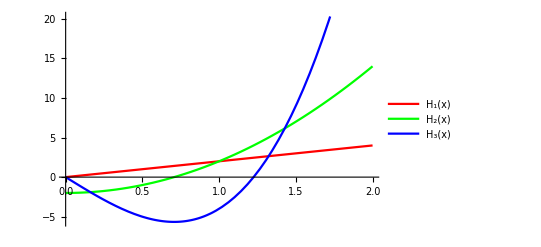

```mathematica
Table[HermiteH[n,x],{n,0,5}]
Table[D[ⅇ^(2x t-t^2),{t,n}]/.t->0,{n,0,5}]
D[HermiteH[n,x],{x,2}]-2 x D[HermiteH[n,x],{x,1}]+2n HermiteH[n,x]==0//FullSimplify
Plot[{HermiteH[1,x],HermiteH[2,x],HermiteH[3,x]},{x,0,2},PlotStyle->{Red, Green,Blue},PlotLegends->Placed["Expressions",{0.25,0.75}]]
```

例题：试证明：如果 f(z) 在上半平面解析，且 lim_(z→∞) f(z)=0 在 0≤arg z≤π 一致成立，则：

f(z)在上半平面的值完全由其实轴上的实部或虚部值确定。

说明：对解析函数，由 C-R 条件（共轭性质），人们可以由实部确定虚部（或反之），

由 Cauchy定理，人们可以由边界值（实部与虚部）确定内部值，

本题说明：在一定条件下，只要知道边界上的实部或虚部，就可确定内部的函数值。

-Graphics-

证明：由Cauchy公式，对复平面上的两个点 z,z^* （其中 z 为上半平面上的一点， z^* 为 z 的复共轭）有

f(z)=1/(2π ⅈ)∳_C (f(ξ))/(ξ-z)ⅆξ,  C 为上图红色路径（实轴和圆心于原点半径 R 的上半圆周构成的回路）

0=1/(2π ⅈ)∳_C (f(ξ))/(ξ-z^*)ⅆξ，因为回路内被积函数解析

两式相减：f(z)=1/(2π ⅈ)∳_C f(ξ)[1/(ξ-z)-1/(ξ-z^*)]ⅆξ,  令： z=x+ⅈ y,  z^*=x-ⅈ y

f(z)=1/(2π ⅈ)∳_C (f(ξ)2ⅈ y)/((ξ-z)(ξ-z^*))ⅆξ=1/(2π ⅈ)∫_-R^R (f(ξ)2ⅈ y)/((ξ-z)(ξ-z^*))ⅆξ=y/π∫_-R^R (f(ξ))/((ξ-z)(ξ-z^*))ⅆξ

其中利用了大圆弧引理：∫_C_R =0

(1.EquationNumbered)式分别求实部和虚部，ξ=ζ+ⅈ η，在实轴上：ξ=ζ,   (ξ-z)(ξ-z^*)=[(ζ-x)-ⅈ y][(ζ-x)+ⅈ y]

u(x,y)=y/π∫_(-∞)^(+∞) (u(ζ,0)ⅆζ)/((ζ-x)^2+y^2)          实轴上的实部确定了上半平面任一点的实部

v(x,y)=y/π∫_(-∞)^(+∞) (v(ζ,0)ⅆζ)/((ζ-x)^2+y^2)          实轴上的虚部确定了上半平面任一点的虚部

(1.EquationNumbered) 与 (1.EquationNumbered)两式相加

f(z)=1/(2π ⅈ)∳_C f(ξ)[1/(ξ-z)+1/(ξ-z^*)]ⅆξ

f(z)=1/(2π ⅈ)∳_C (f(ξ)(2ξ-2x))/((ξ-z)(ξ-z^*))ⅆξ=1/(2π ⅈ)∫_-R^R (f(ζ)(2ζ-2x))/((ζ-x)^2+y^2)ⅆξ

分别求实部和虚部，ξ=ζ+ⅈ η

u(x,y)=1/π∫_(-∞)^(+∞) (v(ζ,0)(ζ-x)ⅆζ)/((ζ-x)^2+y^2)       实轴上的虚部确定了上半平面任一点的实部

v(x,y)=-1/π∫_(-∞)^(+∞) (u(ζ,0)(ζ-x)ⅆζ)/((ζ-x)^2+y^2)    实轴上的实部确定了上半平面任一点的虚部

例题：试证明：对解析函数，圆周上的实部（虚部）就确定了圆内的实部（虚部）。

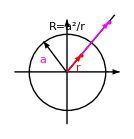
证明：由Cauchy公式，
对复平面上的两个点 z, z'=a^2 ⅇ^(ⅈ arg z)/|z|  
（ z 与 z' 构成圆的一对对称点 ，如右图）
若圆内 z 点放置一点电荷，
圆外的 z' 点实际上就是像电荷位置所在的点
f(z)=1/(2π ⅈ)∳_C_a (f(ξ))/(ξ-z)ⅆξ,     z=r ⅇ^(ⅈ ϕ),   ξ=a ⅇ^(ⅈ θ)
f(r ⅇ^(ⅈ ϕ))=1/(2π)∫_0^(2π) (f(a ⅇ^(ⅈ θ))a ⅇ^(ⅈ θ)ⅆθ)/(a ⅇ^(ⅈ θ)-r ⅇ^(ⅈ ϕ))               (a)            -Graphics-

0=1/(2π ⅈ)∳_C_a (f(ξ))/(ξ-z')ⅆξ      因为 z' 为圆外的点，被积函数在 C_a 内解析

0=1/(2π)∫_0^(2π) (f(a ⅇ^(ⅈ θ))a ⅇ^(ⅈ θ)ⅆθ)/(a ⅇ^(ⅈ θ)-(a^2/r) ⅇ^(ⅈ ϕ))=1/(2π)∫_0^(2π) (f(a ⅇ^(ⅈ θ))r ⅇ^(ⅈ θ)ⅆθ)/(r ⅇ^(ⅈ θ)-a ⅇ^(ⅈ ϕ))               (b)

(a), (b) 两式相减

f(r ⅇ^(ⅈ ϕ))=1/(2π)∫_0^(2π) f(a ⅇ^(ⅈ θ))[(a ⅇ^(ⅈ θ)ⅆθ)/(a ⅇ^(ⅈ θ)-r ⅇ^(ⅈ ϕ))-(r ⅇ^(ⅈ θ)ⅆθ)/(r ⅇ^(ⅈ θ)-a ⅇ^(ⅈ ϕ))]ⅆθ
=1/(2π)∫_0^(2π) (a^2-r^2)/(a^2+r^2-2r a cos(θ-ϕ))f(a ⅇ^(ⅈ θ))ⅆθ

圆周上的实部（虚部）确定了圆内的实部（虚部）

```mathematica
tst=(a ⅇ^(ⅈ θ))/(a ⅇ^(ⅈ θ)-r ⅇ^(ⅈ ϕ))-(r ⅇ^(ⅈ θ))/(r ⅇ^(ⅈ θ)-a ⅇ^(ⅈ ϕ));
Simplify[ComplexExpand[Re[tst]]]
Simplify[ComplexExpand[Im[tst]]]
```

(a^2-r^2)/(a^2+r^2-2 a r Cos[θ-ϕ])

0

把上半平面的函数值表为实轴函数值的积分形式称为上半平面的泊松公式

把圆内的函数值表为圆周函数值的积分形式称为圆内区域的泊松公式

对称点：设圆半径为 a，从圆心 c 作一条射线，在射线上取两点 z_1, z_2

若 |z_1-c||z_2-c|=a^2，则称 z_1, z_2 为圆的一对对称点。

例如： z 与 z'=a^2 ⅇ^(ⅈ arg z)/|z|   构成圆心于原点半径为 a 的圆的一对对称点

例题：计算

I =∳_C (z+1/z)^(2n)ⅆz/z=∳(z^2+1)^(2n)ⅆz/z^(2n+1)，  C 为中心于原点的单位圆一周

解：利用高阶导数Cauchy公式： I=(2π ⅈ)/((2n)!)f^(2n)(0)

f(z)=(z^2+1)^(2n)=(∑_(k=0))^(2n)(C_k^(2n)(z^2))^k

f^(2n)(0)=C_n^(2n)(2n)! =[((2n)!)/(n!)]^2

利用此式可计算：∫_0^(2π) cos^(2n)θⅆθ   （怎么计算？）

此题仅用于理解高阶导数Cauchy公式，实际上可用留数定理计算之。

例题：计算

I=∫_0^∞ ⅇ^(- a x^2)cos b x ⅆx,   其中 a>0

解：cos b x 为偶函数，不妨设 b>0,  并利用：cos b x =1/2(ⅇ^(ⅈ b x)+ⅇ^(- ⅈ b x))

I=1/2∫_(-∞)^∞ ⅇ^(-a x^2)cos b x ⅆx=1/2 Re ∫_(-∞)^∞ ⅇ^(-a x^2)ⅇ^(ⅈ b x) ⅆx=1/2 Re I'

ⅇ^(ⅈ b z)形式诱使利用 Jordan 引理，增添下图所示红色路径 C_R，f(z)=ⅇ^(-a z^2)ⅇ^(ⅈ b z)

引理条件是在上半平面，满足： lim_(z→∞) f(z)=0  （一致成立）

但当 z 沿虚轴趋于无穷时，f(z)=ⅇ^(-a z^2)不趋于0，不满足引理的条件。

-Graphics-

选如上图蓝色路径，f(z)=ⅇ^(-a z^2)ⅇ^(ⅈ b z)

I'=∫_(-∞)^∞ ⅇ^(-a x^2)ⅇ^(ⅈ b x) ⅆx=lim_(R→∞) ∫_l_1 f(z) ⅆz,  其中 l_1 为沿实轴从 -R 到 R

因为 f(z)解析,  ∫_l_1 +∫_l_2 +∫_l_3 +∫_l_4=0   ⟹   ∫_l_1=-[∫_l_2 +∫_l_3 +∫_l_4]

l_2：z=R+ⅈ y,   ⅆz=ⅈ ⅆy,  R→∞ 时

∫_l_2 ⅇ^(-a z^2)ⅇ^(ⅈ b z)ⅆz=ⅈ∫_0^h ⅇ^(-a R^2- 2ⅈ a y + a y^2 + ⅈ b R- b y)ⅆy=0

同理：∫_l_4 f(z)ⅆz=0    ⟹   ∫_l_1 f(z)ⅆz=-∫_l_3 f(z)ⅆz

——    把沿实轴的积分路线平移到上半平面，貌似更为复杂

l_3：z=x +ⅈ h,    x 从  R  到  -R，代入    ∫_l_3 f(z)ⅆz ，   f(z)=ⅇ^(-a z^2)ⅇ^(ⅈ b z)

I_3=∫_l_3 ⅇ^(-a z^2)ⅇ^(ⅈ b z)ⅆz=∫_-R^R ⅇ^(-a (x^2+ 2ⅈ h x -h^2) + ⅈ b (x + ⅈ h))ⅆx
=∫_-R^R ⅇ^(-a (x^2 -h^2) -b h+ ⅈ x (b- 2h a))ⅆx

选取适当的 h，使得指数上虚部等于 0，h=b/(2a)，这时积分化为   ∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx 形式

I_3=∫_(-∞)^∞ ⅇ^(-a x^2+ a h^2 - b h)ⅆx=ⅇ^(a h^2-b h)∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx
=ⅇ^(a h^2-b h)√(π/a)=ⅇ^(-b^2/(4 a^2))√(π/a)，其中利用了：∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx=√(π/a)

试由此推出：

∫_(-∞)^∞ ⅇ^(-a (x-β)^2) ⅆx=√(π/a),        β 可以是任意复常数（a>0）。

```mathematica
Integrate[Exp[-a (x-b)^2],{x,-∞,∞},Assumptions->a>0]
Integrate[Exp[-a (x-b)^2]/.b->2+3ⅈ,{x,-∞,∞},Assumptions->a>0]
```

(√π)/(√a)

(√π)/(√a)